```mathematica
savedir=SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes"];
```

```mathematica
NotebookSave[EvaluationNotebook[],savedir<>"\\uncertainty_dirichlet"]
```

```mathematica
nn=5*10^6;
```

```mathematica
data=Import["scripts\\dataset1_simple.csv"];
n=Length[data[[;;,1]]];
Dimensions[data]
```

{6029,97}

```mathematica
labels[ng_]:=
SortBy[Tally[data[[;;,Join[{1,2,3},ng]]]],FromDigits[#[[1]],2]&][[;;,1]];ClearAll[fs];fs[ng_]:=fs[ng]=
SortBy[Tally[data[[;;,Join[{1,2,3},ng]]]],FromDigits[#[[1]],2]&][[;;,2]]/n
```

```mathematica
fi=fs[{}]
```

{2427/6029,396/6029,1102/6029,443/6029,627/6029,73/6029,428/6029,533/6029}

```mathematica
listsample:=Block[{rsam=RandomSample[Range[94],25]},FoldList[Join,{rsam[[1]]},T@{rsam[[2;;]]}]]
```

```mathematica
listsample0=listsample;
```

```mathematica
ClearAll[defin,bdistr,lddir,lmaxi,ddir,int1,ddistr];defin[nx_,f_,tx_,f1_,t_]:=(
Print["bdistr"];
bdistr[aa_,x_]=Assuming[0<x<1,PDF[BetaDistribution[nx*f1+aa/t,(nx+aa)-(nx*f1+aa/t)],x]];

Print["lddir"];
lddir[aa_]=(*(Multinomial@@(nx*f))**)LogGamma[aa]-LogGamma[nx+aa]+(Total@LogGamma[nx*f+aa/tx])-Length[f]*LogGamma[aa/tx];

Print["lmaxi"];
lmaxi=({#[[1]],ax/.#[[2]]}&@NMaximize[{lddir[ax](*-Log[ax]*),1<ax<tx},ax,AccuracyGoal->Infinity,PrecisionGoal->4]);

Print["ddir"];
ddir[aa_]=Simplify[(*(Multinomial@@(nx*f))**)Gamma[aa]/Gamma[nx+aa]*(Times@@Gamma[nx*f+aa/tx])/Gamma[aa/tx]^Length[f]];

Print["int1"];
int1=NIntegrate[ddir[ax]/Exp[lmaxi[[1]]],{ax,0,+Infinity},AccuracyGoal->Infinity,PrecisionGoal->2];

Print["ddistr"];
ddistr[x_]:=NIntegrate[bdistr[aa,x]*ddir[aa]/Exp[lmaxi[[1]]],{aa,0,+Infinity},AccuracyGoal->Infinity,PrecisionGoal->2]/int1;
);
```

```mathematica
defin[n,fs[listsample0[[3]]],2^(3+3),fi[[1]],8]
```

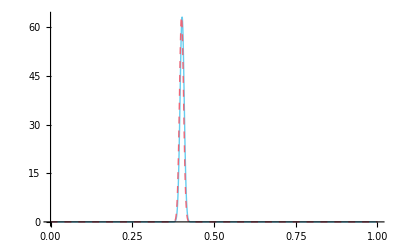

```mathematica
Plot[{bdistr[1,x],ddistr[x]},{x,0,1},PlotRange->All]
```

```mathematica
listsample0=listsample;
```

```mathematica
defin[n,fs[listsample0[[12]]],2^(3+12),fi[[1]],8]
```

```mathematica
int1
```

175.901

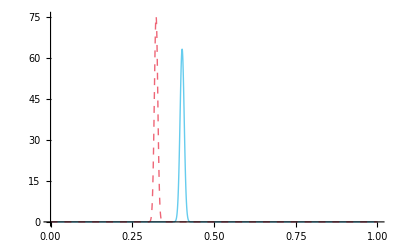

```mathematica
Plot[{bdistr[1,x],ddistr[x]},{x,0,1},PlotRange->All]
```

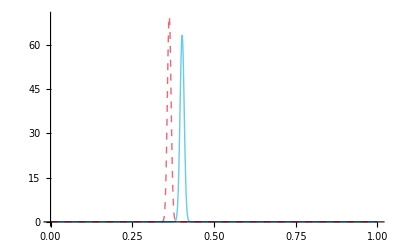

```mathematica
Plot[{bdistr[1,x],bdistr[1000,x]},{x,0,1},PlotRange->All]
```

```mathematica
defin[n,fs[listsample0[[12]]],2^(3+12),1/n,2^12]
```

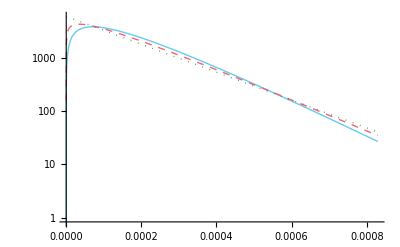

```mathematica
LogPlot[{ddistr[x],bdistr[1000,x],bdistr[1,x]},{x,0,5/n},PlotRange->All]
```

```mathematica
defin[n,fs[listsample0[[12]]],2^(3+12),0,2^12]
```

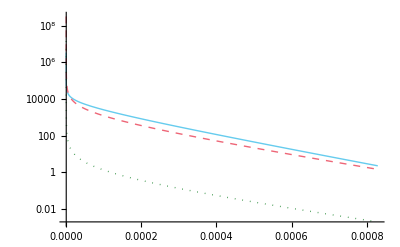

```mathematica
LogPlot[{ddistr[x],bdistr[1000,x],bdistr[1,x]},{x,0,5/n},PlotRange->All]
```

```mathematica
defin[n,fs[listsample0[[3]]],2^(3+3),0,2^(3)]
```

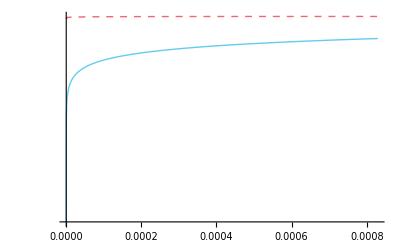

```mathematica
LogPlot[{bdistr[1000,x],ddistr[x]},{x,0,5/n},PlotRange->All]
```

```mathematica
bdistr[10,0.4]
```

0.256398

```mathematica
Exp[lmaxi[[1]]]
```

0.0136129

```mathematica
ddir[aa]//N
```

(Gamma[0.0121081+0.125 aa] Gamma[0.0656825+0.125 aa] Gamma[0.0709902+0.125 aa] Gamma[0.0734782+0.125 aa] Gamma[0.088406+0.125 aa] Gamma[0.103997+0.125 aa] Gamma[0.182783+0.125 aa] Gamma[0.402554+0.125 aa] Gamma[aa])/(Gamma[0.125 aa]^8 Gamma[1.+aa])

```mathematica
int1
```

NIntegrate[ddir[aa]/(aa Exp[lmaxi⟦1⟧]),{aa,0,+∞},AccuracyGoal→∞,PrecisionGoal→2]

```mathematica
lmaxi//N
```

{-4.29674,3.38065}

```mathematica
n
```

```mathematica
ClearAll[bdistr];bdistr[f_,nx_,aa_,t_]:=bdistr[f,nx,aa,t]=Function[Block[{a1=aa+nx,f1=(nx*f+aa/t)/(nx+aa)},PDF[BetaDistribution[a1*f1,a1*(1-f1)],#]]]
```

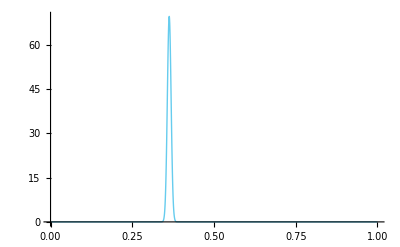

```mathematica
Plot[bdistr[fi[[1]],n,1000,8][x],{x,0,1},PlotRange->All]
```

```mathematica
eprob[f_,nx_,aa_,t_]=(nx*f+aa/t)/(nx+aa)
```

(f nx+aa/t)/(aa+nx)

```mathematica
ddir[n,fi[[1]],8][10]//N
```

7.81637572165121×10^-20201

```mathematica
ClearAll[ddir];ddir[nx_,f_,t_]:=ddir[nx,f,t]=
Function[aa,Evaluate[
(*(Multinomial@@(nx*f))**)Gamma[aa]/Gamma[nx+aa]*(Times@@Gamma[nx*f+aa/t])/Gamma[aa/t]^Length[f]]]
```

```mathematica
ClearAll[lddir];lddir[nx_,f_,t_]:=lddir[nx,f,t]=Function[aa,Evaluate[
(*(Multinomial@@(nx*f))**)LogGamma[aa]-LogGamma[nx+aa]+(Total@LogGamma[nx*f+aa/t])-Length[f]*LogGamma[aa/t]]]
```

```mathematica
ClearAll[lmaxi];lmaxi[f_,tx_]:=lmaxi[f,tx]={#[[1]],ax/.#[[2]]}&@NMaximize[{lddir[n,f,tx][ax]-Log[ax],1<ax<tx},ax,AccuracyGoal->Infinity,PrecisionGoal->4];
```

```mathematica
(*fun[ax_]=Simplify[ddir[n,fr,tx][ax]/ax/maxp];*)
ClearAll[inta,int1];inta[nx_,f_,tx_]:=inta[nx,f,tx]=Block[{maxf=Exp@lmaxi[f,tx][[1]]},NIntegrate[ddir[nx,f,tx][aa]/(nx+aa)/maxf,{aa,0,+Infinity},AccuracyGoal->Infinity,PrecisionGoal->2]];
int1[nx_,f_,tx_]:=int1[nx,f,tx]=Block[{maxf},maxf=Exp[lmaxi[f,tx][[1]]];NIntegrate[Evaluate[ddir[nx,f,tx][aa]]/aa/maxf,{aa,0,+Infinity},AccuracyGoal->Infinity,PrecisionGoal->2]];
```

```mathematica
ClearAll[ddistr];ddistr[f1_,f_,nx_,t_]:=ddistr[f1,f,nx,t]=Function[Block[{ma,ia,i1},
ma=Evaluate[Exp[lmaxi[f,t][[1]]]];
ia=NIntegrate[bdistr[f,nx,aa,t][#]*ddir[nx,f,t][aa]/aa/ma,{aa,0,+Infinity},AccuracyGoal->Infinity,PrecisionGoal->2];
i1=Evaluate[NIntegrate[ddir[nx,f,t][aa]/aa/ma,{aa,0,+Infinity},AccuracyGoal->Infinity,PrecisionGoal->2]];
ia/i1]]
```

```mathematica
ddir[n,fs[listsample0[[1]]],8][ax]
```

(Gamma[22+ax/8] Gamma[51+ax/8] Gamma[121+ax/8] Gamma[126+ax/8] Gamma[139+ax/8] Gamma[156+ax/8] Gamma[176+ax/8] Gamma[270+ax/8] Gamma[295+ax/8] Gamma[304+ax/8] Gamma[307+ax/8] Gamma[377+ax/8] Gamma[451+ax/8] Gamma[683+ax/8] Gamma[807+ax/8] Gamma[1744+ax/8] Gamma[ax])/(Gamma[ax/8]^16 Gamma[6029+ax])

```mathematica
ClearAll[ddistr];ddistr[f1_,f_,nx_,t_]:=ddistr[f1,f,nx,t]=
Function[NIntegrate[bdistr[f1,nx,aa,t][#]*ddir[nx,f,t][aa]/aa/Exp[lmaxi[f,t][[1]]],{aa,0,+Infinity},AccuracyGoal->Infinity,PrecisionGoal->2]/int1[nx,f,t]];
```

```mathematica
int1[n,fs[listsample0[[1]]],8]
```

NIntegrate[1/(aa maxf)Evaluate[ddir[6029,{683/6029,1744/6029,126/6029,270/6029,295/6029,807/6029,139/6029,304/6029,176/6029,451/6029,22/6029,51/6029,121/6029,307/6029,156/6029,377/6029},8][aa]],{aa,0,+∞},AccuracyGoal→∞,PrecisionGoal→2]

```mathematica
ddistr[fs[listsample0[[1]]],10,8]
```

NIntegrate[(bdistr[{683/6029,1744/6029,126/6029,270/6029,295/6029,807/6029,139/6029,304/6029,176/6029,451/6029,22/6029,51/6029,121/6029,307/6029,156/6029,377/6029},10,aa,8][#1] ddir[10,{683/6029,1744/6029,126/6029,270/6029,295/6029,807/6029,139/6029,304/6029,176/6029,451/6029,22/6029,51/6029,121/6029,307/6029,156/6029,377/6029},8][aa])/(aa Exp[lmaxi[{683/6029,1744/6029,126/6029,270/6029,295/6029,807/6029,139/6029,304/6029,176/6029,451/6029,22/6029,51/6029,121/6029,307/6029,156/6029,377/6029},8]⟦1⟧]),{aa,0,+∞},AccuracyGoal→∞,PrecisionGoal→2]/int1[10,{683/6029,1744/6029,126/6029,270/6029,295/6029,807/6029,139/6029,304/6029,176/6029,451/6029,22/6029,51/6029,121/6029,307/6029,156/6029,377/6029},8]&

```mathematica
fs[listsample0[[1]]]
```

{683/6029,1744/6029,126/6029,270/6029,295/6029,807/6029,139/6029,304/6029,176/6029,451/6029,22/6029,51/6029,121/6029,307/6029,156/6029,377/6029}

```mathematica
NIntegrate[ddir[n,fs[listsample0[[1]]],8][aa]/aa/ma,{aa,0,+Infinity},AccuracyGoal->Infinity,PrecisionGoal->2]
```

NIntegrate[(ddir[n,fs[listsample0⟦1⟧],8][aa])/(aa ma),{aa,0,+∞},AccuracyGoal→∞,PrecisionGoal→2]

```mathematica
ddir[n,fi[[1]],8]
```

Function[aa$,(Gamma[aa$] Times@@Gamma[(6029 2427)/6029+aa$/8])/(Gamma[6029+aa$] Gamma[aa$/8]^Length[2427/6029])]

```mathematica
ef[nx_,f_,t_,fx_,tx_]:=f-(f-1/t)*inta[nx,fx,tx]/int1[nx,fx,tx]
```

```mathematica
ef[n,{0,1/n},2^(15),fs[listsample0[[15]]],2^(3+15)]
```

{0.0000188719,0.0000821671}

```mathematica
tef=ef[n,fi,8,fs[listsample0[[15]]],2^(3+15)]
```

{0.230917,0.102364,0.14705,0.105339,0.116985,0.0819197,0.104389,0.111035}

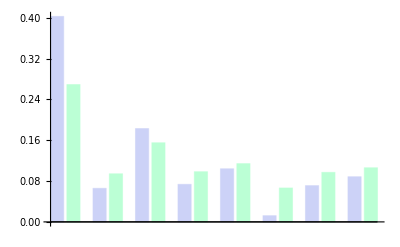

```mathematica
BarChart[T@{fi,tef}]
```

```mathematica
fi//N
```

{0.402554,0.0656825,0.182783,0.0734782,0.103997,0.0121081,0.0709902,0.088406}

```mathematica
cd[aa_]=PDF[CauchyDistribution[Log[1000],Log[100]],aa];
```

```mathematica
ClearAll[ibdistr];ibdistr[f_,nx_,t_]:=ibdistr[f,nx,t]=Function[x,NIntegrate[bdistr[f,nx,aa,t,x]*cd[Log[aa]]/aa,{aa,0,+Infinity}]]
```

```mathematica
ClearAll[ibdistru];ibdistru[f_,nx_,t_]:=ibdistru[f,nx,t]=Function[x,
Block[{maxf=Exp@lmaxi[f,t][[1]]},NIntegrate[bdistr[f,nx,aa,t,x]*ddir[nx,f,t][aa]/maxf/aa,{aa,0,+Infinity},AccuracyGoal->Infinity,PrecisionGoal->2]/NIntegrate[ddir[nx,f,t][aa]/maxf/aa,{aa,0,+Infinity},AccuracyGoal->Infinity,PrecisionGoal->2]]];
```

```mathematica
ibdistru[fi[[1]],n,8][0.25]
```

$Aborted

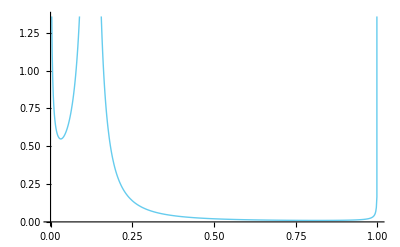

```mathematica
Plot[ibdistr[fi[[1]],,8][x],{x,0,1},PlotRange->Auto,PlotPoints->10]
```

```mathematica
CauchyDistribution
```

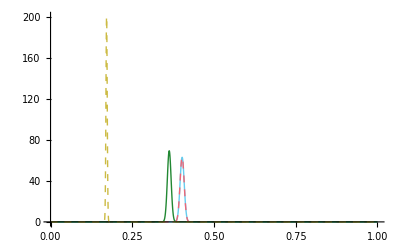

```mathematica
Plot[Evaluate@Table[bdistr[fi[[1]],n,aa,8,x],{aa,{0.1,1,1000,30000}}],{x,0,1},PlotRange->{0,All},PlotStyle->{Auto,Dashed}]
```

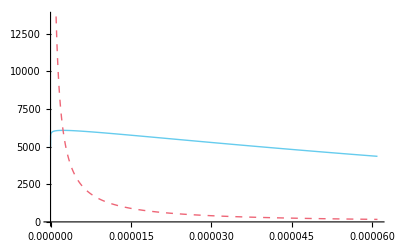

```mathematica
tt=2^15;Plot[Evaluate@Flatten@Table[{bdistr[1/n,n,aa,tt,x],bdistr[0,n,aa,tt,x]},{aa,{500}}],{x,0,2/tt},PlotRange->Auto,PlotStyle->{Auto,Dashed}]
```

```mathematica
eprob[{1/n,0},n,500,tt]
```

{8317/53485568,125/53485568}

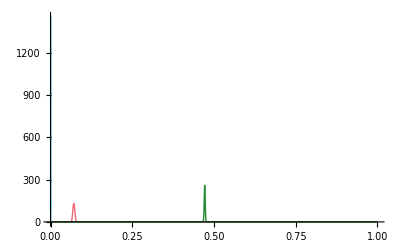

```mathematica
Plot[Evaluate@Table[bdistr[1/n,n,aa,x],{aa,{1,1000,10^5}}],{x,0,1},PlotRange->{0,All}]
```